```mathematica
Keep[sets_,vertex_]:=Block[{result},
result=Map[Select[#,MemberQ[vertex,#]&]&,sets];
result=Select[result,#≠{}&]
]
```

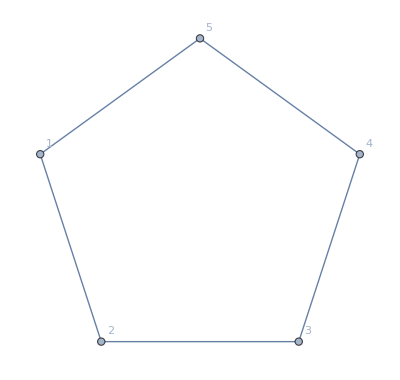

```mathematica
g1=CycleGraph[5,VertexLabels->"Name"]
```

```mathematica
With[{f=Select[FindFullFormula[g1],SymbolLevel[#]≤4&]},
Select[Map[SetsToSymbol[Keep[SymbolToSets[#],{1,2,3,4,5}]]&,f],SymbolLevel[#]==3&]
]//DeleteDuplicates//TableForm
```

v1x24x35
v14x2x35
v14x25x3
v13x25x4
v13x24x5

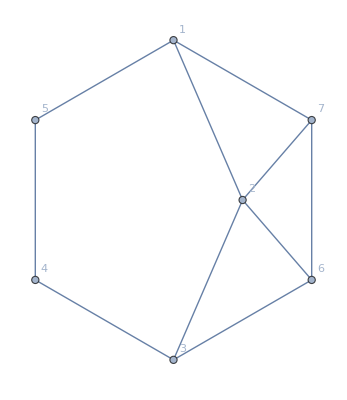

```mathematica
g2=Graph[EdgeAdd[g1,{3<->6,2<->6,1<->7,2<->7,7<->6}],GraphLayout->"TutteEmbedding"]
```

```mathematica
With[{f=Select[FindFullFormula[g2],SymbolLevel[#]≤4&]},
Map[SetsToSymbol[Keep[SymbolToSets[#],{1,2,3,4,5}]]->#&,
Select[f,SymbolLevel[SetsToSymbol[Keep[SymbolToSets[#],{1,7,6,3,4,5}]]]==3&
]
]
]//Sort//TableForm
```

v13x2x4x5→v13x2x46x57
v13x2x4x5→v13x2x47x56
v14x25x3→v146x25x37
v14x2x35→v146x2x35x7
v14x2x35→v14x2x357x6
v14x2x3x5→v146x2x37x5
v14x2x3x5→v146x2x3x57
v14x2x3x5→v14x2x37x56
v1x24x35→v16x24x357
v1x2x35x4→v16x2x357x4
v1x2x35x4→v16x2x35x47
v1x2x35x4→v1x2x357x46

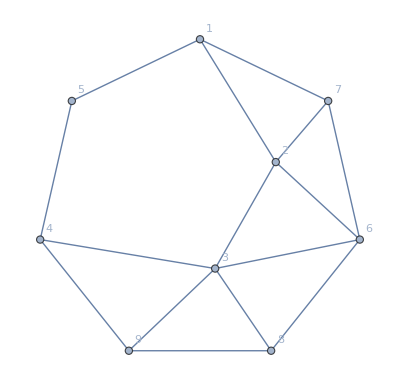

```mathematica
g3=Graph[EdgeAdd[g2,{3<->8,6<->8,3<->9,8<->9,4<->9}],GraphLayout->"TutteEmbedding"]
```

```mathematica
Keep[SymbolToSets[v169x248x357],{1,7,6,8,9,4,5}]
```

{{1,6,9},{4,8},{5,7}}

```mathematica
Sort[{1,7,6,8,9,4,5}]
```

{1,4,5,6,7,8,9}

```mathematica
With[{f=Select[FindFullFormula[g2],SymbolLevel[#]≤4&]},
Map[SetsToSymbol[Keep[SymbolToSets[#],{1,2,3,4,5}]]->#&,
Select[f,SymbolLevel[SetsToSymbol[Keep[SymbolToSets[#],{1,4,5,6,7,8,9}]]]==3&
]
]
]//Sort//TableForm
```

v13x2x4x5→v13x2x46x57
v13x2x4x5→v13x2x47x56
v14x25x3→v146x25x37
v14x25x3→v146x25x3x7
v14x2x35→v146x2x35x7
v14x2x35→v14x2x357x6
v14x2x3x5→v146x2x37x5
v14x2x3x5→v14x2x37x56
v1x24x35→v16x24x357
v1x24x3x5→v16x24x3x57
v1x25x3x4→v16x25x3x47
v1x2x35x4→v16x2x357x4
v1x2x35x4→v16x2x35x47
v1x2x35x4→v1x2x357x46